```mathematica
T = Quantity[300, "Kelvins"];
kb = Quantity["BoltzmannConstant"];
A = Quantity[50, "Nanometers"];
cUp = Quantity[95, "Nanometers"];
P = Quantity[24, "Nanometers"];
omega0 = Quantity[1.85, 1 / "Nanometers"];
c= UnitConvert[kb * T * cUp * omega0^2, "Piconewtons"];
p = UnitConvert[kb * T * P * omega0^2, "Piconewtons"];
f = Quantity[1, "Piconewtons"];
g = UnitConvert[f - Sqrt[kb * T * f / A], "Piconewtons"];
cs = UnitConvert[c (1 - cUp / (4A) * Sqrt[kb * T / (A * f)]), "Piconewtons"];
tau0 = UnitConvert[Sqrt[2 * p * g / (omega0^2 * (1 - p / cs))], "Piconewtons" * "Nanometers"];
tauS =  UnitConvert[cs / omega0, "Piconewtons" * "Nanometers"];
tauP =  UnitConvert[p / omega0, "Piconewtons" * "Nanometers"];
sigmaS = 1 / cs * Sqrt[2 * p * g / (1 - p / cs)];
sigmaP = 1 / p * Sqrt[2 * p * g / (1 - p/cs)];
zRNAP=Quantity[4.42, "Nanometers"];
```

```mathematica
torque[sigma_]:=Piecewise[{{tauS*sigma,Abs[sigma] < Abs[sigmaS]},{tau0 * Sign[sigma] , Abs[sigmaS] ≤ Abs[sigma] ≤ Abs[sigmaP]},{tauP*sigma,Abs[sigmaP]≤ Abs[sigma]}}]
S[sigma_]:=Piecewise[{{-g+cs/2*sigma^2,Abs[sigma] < Abs[sigmaS]},{-g/(1-p/cs)+Sqrt[2p*g/(1-p/cs)]*Abs[sigma] , Abs[sigmaS] ≤ Abs[sigma] ≤ Abs[sigmaP]},{p/2*sigma^2,Abs[sigmaP]≤ Abs[sigma]}}]
bindingEnergy[sigma_]:=torque[sigma]*1.2*2Pi-zRNAP*S[sigma]
bindingEnergyNoBubble[sigma_]:=torque[sigma]*1.2*2Pi
```

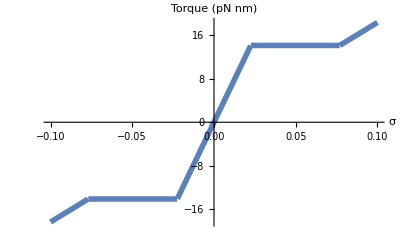

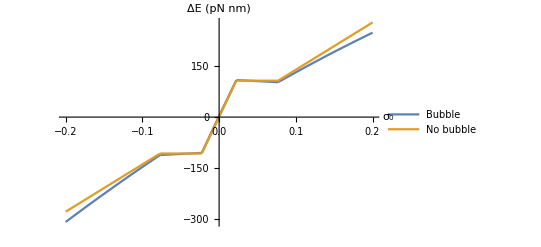

C:\Users\ChemeGrad2019\source\repos\tangles_model\notebooks\delta_energy.csv

```mathematica
Plot[torque[sigma],{sigma,-.1,.1},AxesLabel->{"σ","Torque (pN nm)"}, BaseStyle->{FontSize->16, FontFamily->"Helvetica Neue", FontColor->Black},PlotStyle->Thickness[.01]]
ePlot = Plot[{UnitConvert[bindingEnergy[sigma], "Piconewtons" * "Nanometers"],UnitConvert[bindingEnergyNoBubble[sigma], "Piconewtons" * "Nanometers"]},{sigma,-.2,.2},AxesLabel->{"σ_0","ΔE (pN nm)"},PlotLegends->{"Bubble","No bubble"}]
Export[NotebookDirectory[]<>"delta_energy.csv",Table[{sigma, QuantityMagnitude[UnitConvert[bindingEnergy[sigma], "Piconewtons" * "Nanometers"]], QuantityMagnitude[UnitConvert[bindingEnergyNoBubble[sigma], "Piconewtons" * "Nanometers"]]}, {sigma,-0.2,0.2, 0.01}], "CSV"]
```